# Lab 5 William Keilsohn Section 32 3/27/2014

```mathematica
Quit[]
```

Question 1: Define f(x) and plot on [-1,3]

```mathematica
f[x_]=(x^4)-(2*x^3)-(x^2)-2*x+2
```

2-2 x-x^2-2 x^3+x^4

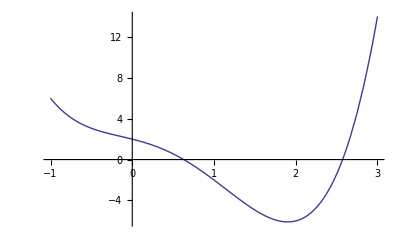

```mathematica
Plot[f[x],{x,-1,3}]
```

Question 1.a: How many Roots are on The interval?

```mathematica
Factor[f[x]]
```

2-2 x-x^2-2 x^3+x^4

There are Two Roots on the interval [-1,3]

Question 1.b: By zooming in, determine the left root accurate to four decemil places.

Additional Plots removed upon request of prompt.

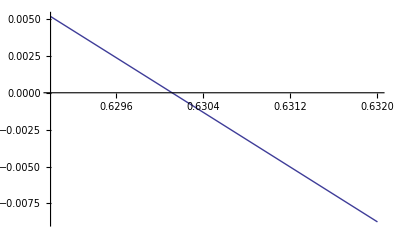

```mathematica
Plot[f[x],{x,0.629,0.632}]
```

Therefore, the left root is approximatily 0.6301. 

Question 1.c: Evaluate f at this value. How close is it to zero?

```mathematica
f[0.6301]
```

0.0000714648

The value of f is 0.0000714648 and is 0.0000714648 units away from zero.

Question 2: Use bisection method to find this root.

```mathematica
a=0.0;b=1.0;m=(a+b)/2;output={{m,f[m]}}
While[b-a>10^(-5),If[Sign[f[a]]≠Sign[f[m]],b=m,a=m];m=(a+b)/2;output=Append[output,{m,f[m]}]];
```

{{0.5,0.5625}}

```mathematica
output//TableForm
```

0.5 | 0.5625
0.75 | -0.589844
0.625 | 0.0236816
0.6875 | -0.274155
0.65625 | -0.122939
0.640625 | -0.0490474
0.632813 | -0.0125368
0.628906 | 0.00560907
0.630859 | -0.0034547
0.629883 | 0.00107947
0.630371 | -0.00118705
0.630127 | -0.000053645
0.630005 | 0.000512948
0.630066 | 0.00022966
0.630096 | 0.0000880099
0.630112 | 0.000017183
0.630119 | -0.0000182309
0.630116 | -5.23913×10^-7

Based on bisection method the left root occurs at x= 0.630116 and results in a f values of -5.23913x10^(-7) witch is closer to zero than previously determined.

Question 3.a: Use newton’s method to find the left root at f(x)=0. Assume x0=0.0 and name all following approximations

```mathematica
newt[t_]=t-f[t]/f'[t]
```

t-(2-2 t-t^2-2 t^3+t^4)/(-2-2 t-6 t^2+4 t^3)

```mathematica
NestList[newt,0.0,10]//TableForm
```

0.
1.
0.666667
0.630769
0.630116
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115

X0= 0.0
X1= 1.0
X2=0.666667
X3=0.630769
X4=0.630116
X5= 0.630115
No further Change in Values derived.

```mathematica
N[NestList[newt,0.0,10],8]//TableForm
```

```mathematica
N[{{0.}, {1.}, {0.6666666666666667}, {0.6307692307692307}, {0.6301156168428664}, {0.6301153961638684}, {0.6301153961638432}, {0.6301153961638432}, {0.6301153961638432}, {0.6301153961638432}, {0.6301153961638432}},8]//TableForm
```

0.
1.
0.666667
0.630769
0.630116
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115

The left root is located at X=0.63011540  when calculated to 8 decimal places.

Question 3.b: What is the f value?

```mathematica
f[NestList[newt,0.0,10]]//TableForm
```

2.
-2.
-0.17284
-0.00303597
-1.02434×10^-6
-1.16962×10^-13
5.55112×10^-17
5.55112×10^-17
5.55112×10^-17
5.55112×10^-17
5.55112×10^-17

```mathematica
f[0.63011540]
```

-1.78065×10^-8

The value of f at the root is -1.78065×10^-8

Question 3.c: Explore what happens when X0 is of a value other than 0. Write your conlcusions.

```mathematica
NestList[newt,1.9,10]//TableForm
```

1.9
-252.096
-188.948
-141.588
-106.068
-79.4288
-59.4504
-44.4678
-33.2324
-24.8079
-18.4921

```mathematica
NestList[newt,1.9,30]//TableForm
```

1.9
-252.096
-188.948
-141.588
-106.068
-79.4288
-59.4504
-44.4678
-33.2324
-24.8079
-18.4921
-13.7585
-10.2122
-7.55688
-5.5701
-4.084
-2.97062
-2.1295
-1.47514
-0.916756
-0.284705
0.979991
0.664367
0.630692
0.630116
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115

```mathematica
NestList[newt,0.5,10]//TableForm
```

0.5
0.640625
0.630172
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115
0.630115

From what I can gather, the farther the value of X0 is from the root, the more values are generated before reaching the correct, or most accurate, value for the root. This is demonstrated in the work above in which X0=1.9 and X0= 0.5.

```mathematica
Quit[]
```